-Graphics-

#### The differential equation is the following:

ϕ^(..)(t)=-g/Rsin(ϕ(t))

WolframAlphaQueryParseResults

π/9 rad

```mathematica
s=NDSolve[{Φ''[t]+(9.85/5)*Sin[Φ[t]]==0,Φ[0]==Pi/9,Φ'[0]==0},Φ,{t,0,12}]
```

{{Φ→InterpolatingFunction[{{0., 12.}}, <>]}}

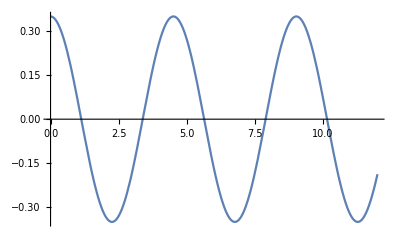

```mathematica
Plot[Evaluate[Φ[t]/.s],{t,0,12},PlotStyle->Automatic]
```

#### The approximation for the solution of the previous equation is the following:

ϕ(t)=Cos(√(g/R))ϕ_0(t)

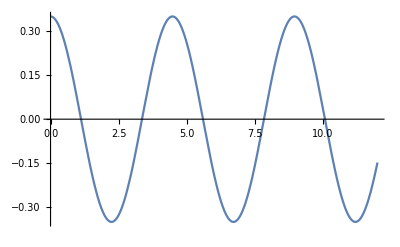

```mathematica
Plot[(Pi/9)*Cos[Sqrt[9.85/5]t],{t,0,12},PlotStyle->Automatic]
```

#### Compare the solutions

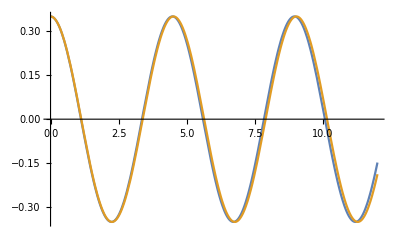

```mathematica
Plot[{(Pi/9)*Cos[Sqrt[9.85/5]t],Evaluate[Φ[t]/.s]},{t,0,12},PlotStyle->Automatic]
```